## Exam 3

## Problem 1

```mathematica
h=6.626*^-34;
c=3*^8;
T=5800;
k=1.381*^-23;
I1=NIntegrate[1/(λ^5 (ⅇ^(h c/(λ k T))-1)),{λ,400 10^-9,500 10^-9}];
I2=NIntegrate[1/(λ^5 (ⅇ^(h c/(λ k T))-1)),{λ,600 10^-9,700 10^-9}];
I2/I1
```

0.892997

## Problem 2

### Part a.

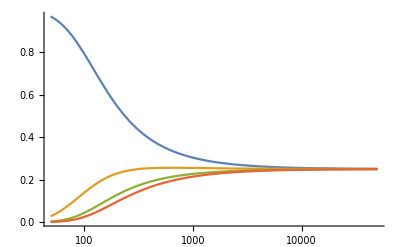

```mathematica
k=8.617*^-5;
z[T_]:=1+ⅇ^((-15*^-3)/(k T))+ⅇ^((-25*^-3)/(k T))+ⅇ^((-3*^-2)/(k T))
P[e_,T_]:=1/z[T] ⅇ^(-e/(k T))
LogLinearPlot[{P[0,T],P[.015,T],P[.025,T],P[.03,T]},{T,0,5*^4},PlotRange->All]
```

### Part b.

```mathematica
T=0.01/(k Log[3])
P[0,T]
P[0.03,T]
```

105.633

0.773014

0.0286302

### Part c.

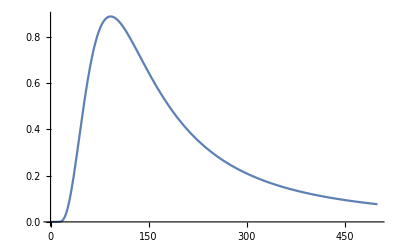

{0.887507,{T→91.9626}}

{T→195.775}

{T→47.8131}

```mathematica
Clear[T]
heatCap[T_]=1/k D[(.015 ⅇ^((-.015)/(k T))+.025 ⅇ^((-.025)/(k T))+.03 ⅇ^((-.03)/(k T)))/(1+ⅇ^((-.015)/(k T))+ⅇ^((-.025)/(k T))+ⅇ^((-.03)/(k T))),T];
Plot[heatCap[T],{T,0,500}]
max=FindMaximum[heatCap[T],{T,100}]
FindRoot[heatCap[T]-max⟦1⟧/2,{T,200}]
FindRoot[heatCap[T]-max⟦1⟧/2,{T,42}]
```

## Problem 3

```mathematica
Integrate[(x^4 ⅇ^x)/((ⅇ^x-1)^2),{x,0,Infinity}]
```

(4 π^4)/15

## Problem 4

```mathematica
Integrate[2/(√π)√x ⅇ^-x,{x,0,Infinity}]-Integrate[2/(√π)√x ⅇ^-x,{x,0,4}]//N
```

0.0460117

## Problem 5

```mathematica
Clear[T,c]
k=1.381*^-23;
integral=Integrate[1/(ⅇ^x+1),x];
Solve[(integral/.x->0)-(integral/.x->μ/(k T))==1/(2 c),T]
Solve[ⅇ^((1/(2c)+μ)/k)-2 ⅇ^(-μ/k)==2^T,T]
1/k
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→-(7.24113×10^22 μ)/Log[-1.+2. ⅇ^(0.5/c)]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→1.4427 Log[-2. ⅇ^(-7.24113×10^22 μ)+ⅇ^(7.24113×10^22 (0.5/c+μ))]}}

7.24113×10^22

## Problem 6

```mathematica
c=3*^8;
xval[T_,λ_]:=(h c)/(λ k T)
integral=-15/π^4 NIntegrate[x^3/(ⅇ^x-1),{x,xval[17394.35,400*^-9],xval[17394.35,750*^-9]}]
```

0.15

## Problem 7

```mathematica
h=6.626*^-34;
T=√10;
c=5*^-3*T;
n=6.022*^23;
m=196.97/(6.022*^26);
k=1.381*^-23;
nOvV=19.3/(196.97*^-6);
ef=h^2/(8 m)((3 nOvV)/π)^(2/3);
γ=(π^2 n k^2)/(2 ef);
Td=CubeRoot[(12k π^4 n T^3)/(5(c-γ T)) ]
(2 k Td)/h
```

-0.0000228067

-950680.